```mathematica
xx:=(d^2-rb^2+ra^2)/(2*d)
```

```mathematica
yy:=ra*Sqrt[1-(xx/ra)^2]
```

```mathematica
xx//OutputForm
```

2     2     2
d  + ra  - rb
--------------
     2 d

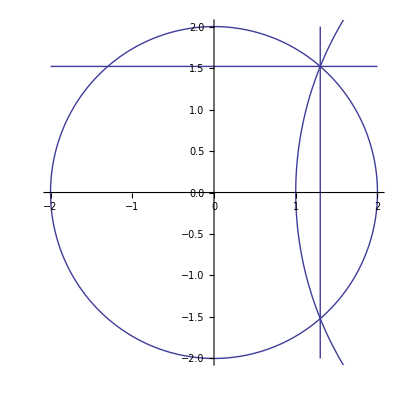

```mathematica
Show[ParametricPlot[{ra*Cos[t],ra*Sin[t]}/.{ra->2},{t,0,2*π}],ParametricPlot[{rb*Cos[t]+d,rb*Sin[t]}/.{rb->4,d->5},{t,0,2*π}],ParametricPlot[{xx,t}/.{ra->2,rb->4,d->5},{t,-2,2}],ParametricPlot[{t,yy}/.{ra->2,rb->4,d->5},{t,-2,2}]]
```

```mathematica
vrs:={ra->3,rb->2.5,d->4}
```

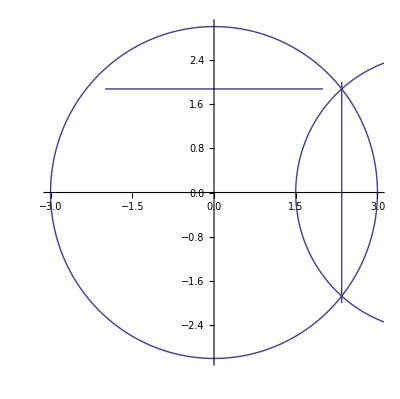

```mathematica
Show[ParametricPlot[{ra*Cos[t],ra*Sin[t]}/.vrs,{t,0,2*π}],ParametricPlot[{rb*Cos[t]+d,rb*Sin[t]}/.vrs,{t,0,2*π}],ParametricPlot[{xx,t}/.vrs,{t,-2,2}],ParametricPlot[{t,yy}/.vrs,{t,-2,2}]]
```

```mathematica
Manipulate[Show[ParametricPlot[{ra*Cos[t],ra*Sin[t]}/.vrs,{t,0,2*π}],ParametricPlot[{yy*Cos[t]*Cos[θ]+xx*Sin[θ],yy*Sin[t]}/.vrs,{t,0,2*π}],PlotRange->{{0,4},{-4,4}}],{θ,0,π/2}]
```

```mathematica
soln=Solve[{ra*Cos[θ]+rbx*Cos[ϕ]==d,ra*Sin[θ]==rby*Sin[ϕ]},{θ,ϕ}]
```

{{θ→ConditionalExpression[ArcTan[(-d ra rby^2-√(ra^4 rbx^4+d^2 ra^2 rbx^2 rby^2-ra^4 rbx^2 rby^2-ra^2 rbx^4 rby^2+ra^2 rbx^2 rby^4))/(ra^2 rbx^2-ra^2 rby^2),-(√(-d^2 rby^2-ra^2 rby^2+rbx^2 rby^2-(2 d^2 ra^2 rby^4)/(ra^2 rbx^2-ra^2 rby^2)-(2 d ra rby^2 √(ra^2 rbx^2 (ra^2 rbx^2+d^2 rby^2-ra^2 rby^2-rbx^2 rby^2+rby^4)))/(ra^2 rbx^2-ra^2 rby^2)))/(√(ra^2 rbx^2-ra^2 rby^2))]+2 π C[1],C[1]∈Integers],ϕ→ConditionalExpression[ArcTan[(d+(d ra^2 rby^2)/(ra^2 rbx^2-ra^2 rby^2)+(ra √(ra^2 rbx^2 (ra^2 rbx^2+d^2 rby^2-ra^2 rby^2-rbx^2 rby^2+rby^4)))/(ra^2 rbx^2-ra^2 rby^2))/rbx,-(ra √(-d^2 rby^2-ra^2 rby^2+rbx^2 rby^2-(2 d^2 ra^2 rby^4)/(ra^2 rbx^2-ra^2 rby^2)-(2 d ra rby^2 √(ra^2 rbx^2 (ra^2 rbx^2+d^2 rby^2-ra^2 rby^2-rbx^2 rby^2+rby^4)))/(ra^2 rbx^2-ra^2 rby^2)))/(rby √(ra^2 rbx^2-ra^2 rby^2))]+2 π C[2],C[2]∈Integers]},{θ→ConditionalExpression[ArcTan[(-d ra rby^2-√(ra^4 rbx^4+d^2 ra^2 rbx^2 rby^2-ra^4 rbx^2 rby^2-ra^2 rbx^4 rby^2+ra^2 rbx^2 rby^4))/(ra^2 rbx^2-ra^2 rby^2),(√(-d^2 rby^2-ra^2 rby^2+rbx^2 rby^2-(2 d^2 ra^2 rby^4)/(ra^2 rbx^2-ra^2 rby^2)-(2 d ra rby^2 √(ra^2 rbx^2 (ra^2 rbx^2+d^2 rby^2-ra^2 rby^2-rbx^2 rby^2+rby^4)))/(ra^2 rbx^2-ra^2 rby^2)))/(√(ra^2 rbx^2-ra^2 rby^2))]+2 π C[1],C[1]∈Integers],ϕ→ConditionalExpression[ArcTan[(d+(d ra^2 rby^2)/(ra^2 rbx^2-ra^2 rby^2)+(ra √(ra^2 rbx^2 (ra^2 rbx^2+d^2 rby^2-ra^2 rby^2-rbx^2 rby^2+rby^4)))/(ra^2 rbx^2-ra^2 rby^2))/rbx,(ra √(-d^2 rby^2-ra^2 rby^2+rbx^2 rby^2-(2 d^2 ra^2 rby^4)/(ra^2 rbx^2-ra^2 rby^2)-(2 d ra rby^2 √(ra^2 rbx^2 (ra^2 rbx^2+d^2 rby^2-ra^2 rby^2-rbx^2 rby^2+rby^4)))/(ra^2 rbx^2-ra^2 rby^2)))/(rby √(ra^2 rbx^2-ra^2 rby^2))]+2 π C[2],C[2]∈Integers]},{θ→ConditionalExpression[ArcTan[(-d ra rby^2+√(ra^4 rbx^4+d^2 ra^2 rbx^2 rby^2-ra^4 rbx^2 rby^2-ra^2 rbx^4 rby^2+ra^2 rbx^2 rby^4))/(ra^2 rbx^2-ra^2 rby^2),-(√(-d^2 rby^2-ra^2 rby^2+rbx^2 rby^2-(2 d^2 ra^2 rby^4)/(ra^2 rbx^2-ra^2 rby^2)+(2 d ra rby^2 √(ra^2 rbx^2 (ra^2 rbx^2+d^2 rby^2-ra^2 rby^2-rbx^2 rby^2+rby^4)))/(ra^2 rbx^2-ra^2 rby^2)))/(√(ra^2 rbx^2-ra^2 rby^2))]+2 π C[1],C[1]∈Integers],ϕ→ConditionalExpression[ArcTan[(d+(d ra^2 rby^2)/(ra^2 rbx^2-ra^2 rby^2)-(ra √(ra^2 rbx^2 (ra^2 rbx^2+d^2 rby^2-ra^2 rby^2-rbx^2 rby^2+rby^4)))/(ra^2 rbx^2-ra^2 rby^2))/rbx,-(ra √(-d^2 rby^2-ra^2 rby^2+rbx^2 rby^2-(2 d^2 ra^2 rby^4)/(ra^2 rbx^2-ra^2 rby^2)+(2 d ra rby^2 √(ra^2 rbx^2 (ra^2 rbx^2+d^2 rby^2-ra^2 rby^2-rbx^2 rby^2+rby^4)))/(ra^2 rbx^2-ra^2 rby^2)))/(rby √(ra^2 rbx^2-ra^2 rby^2))]+2 π C[2],C[2]∈Integers]},{θ→ConditionalExpression[ArcTan[(-d ra rby^2+√(ra^4 rbx^4+d^2 ra^2 rbx^2 rby^2-ra^4 rbx^2 rby^2-ra^2 rbx^4 rby^2+ra^2 rbx^2 rby^4))/(ra^2 rbx^2-ra^2 rby^2),(√(-d^2 rby^2-ra^2 rby^2+rbx^2 rby^2-(2 d^2 ra^2 rby^4)/(ra^2 rbx^2-ra^2 rby^2)+(2 d ra rby^2 √(ra^2 rbx^2 (ra^2 rbx^2+d^2 rby^2-ra^2 rby^2-rbx^2 rby^2+rby^4)))/(ra^2 rbx^2-ra^2 rby^2)))/(√(ra^2 rbx^2-ra^2 rby^2))]+2 π C[1],C[1]∈Integers],ϕ→ConditionalExpression[ArcTan[(d+(d ra^2 rby^2)/(ra^2 rbx^2-ra^2 rby^2)-(ra √(ra^2 rbx^2 (ra^2 rbx^2+d^2 rby^2-ra^2 rby^2-rbx^2 rby^2+rby^4)))/(ra^2 rbx^2-ra^2 rby^2))/rbx,(ra √(-d^2 rby^2-ra^2 rby^2+rbx^2 rby^2-(2 d^2 ra^2 rby^4)/(ra^2 rbx^2-ra^2 rby^2)+(2 d ra rby^2 √(ra^2 rbx^2 (ra^2 rbx^2+d^2 rby^2-ra^2 rby^2-rbx^2 rby^2+rby^4)))/(ra^2 rbx^2-ra^2 rby^2)))/(rby √(ra^2 rbx^2-ra^2 rby^2))]+2 π C[2],C[2]∈Integers]}}

```mathematica
qa=√(ra^4 rbx^4+d^2 ra^2 rbx^2 rby^2-ra^4 rbx^2 rby^2-ra^2 rbx^4 rby^2+ra^2 rbx^2 rby^4)
```

√(ra^4 rbx^4+d^2 ra^2 rbx^2 rby^2-ra^4 rbx^2 rby^2-ra^2 rbx^4 rby^2+ra^2 rbx^2 rby^4)

```mathematica
qb=-d ra rby^2
```

-d ra rby^2

```mathematica
qc=ra^2 rbx^2-ra^2 rby^2
```

ra^2 rbx^2-ra^2 rby^2

```mathematica
qd=(2 d ra rby^2 √(ra^2 rbx^2 (ra^2 rbx^2+d^2 rby^2-ra^2 rby^2-rbx^2 rby^2+rby^4)))/(ra^2 rbx^2-ra^2 rby^2)
```

(2 d ra rby^2 √(ra^2 rbx^2 (ra^2 rbx^2+d^2 rby^2-ra^2 rby^2-rbx^2 rby^2+rby^4)))/(ra^2 rbx^2-ra^2 rby^2)

```mathematica
qe=-d^2 rby^2-ra^2 rby^2+rbx^2 rby^2-(2 d^2 ra^2 rby^4)/(ra^2 rbx^2-ra^2 rby^2)
```

-d^2 rby^2-ra^2 rby^2+rbx^2 rby^2-(2 d^2 ra^2 rby^4)/(ra^2 rbx^2-ra^2 rby^2)

```mathematica
qf=(ra √(ra^2 rbx^2 (ra^2 rbx^2+d^2 rby^2-ra^2 rby^2-rbx^2 rby^2+rby^4)))/(ra^2 rbx^2-ra^2 rby^2)
```

(ra √(ra^2 rbx^2 (ra^2 rbx^2+d^2 rby^2-ra^2 rby^2-rbx^2 rby^2+rby^4)))/(ra^2 rbx^2-ra^2 rby^2)

```mathematica
qg=d+(d ra^2 rby^2)/(ra^2 rbx^2-ra^2 rby^2)
```

d+(d ra^2 rby^2)/(ra^2 rbx^2-ra^2 rby^2)

```mathematica
soln[[1,1,2,1,1]]==ArcTan[(qb-qa)/qc,-Sqrt[qe-qd]/Sqrt[qc]]
```

True

```mathematica
soln[[1,2,2,1,1]]==ArcTan[(qg+qf)/rbx,(ra/rby)*(-Sqrt[qe-qd]/Sqrt[qc])]
```

True

```mathematica
soln[[2,1,2,1,1]]==ArcTan[(qb-qa)/qc,Sqrt[qe-qd]/Sqrt[qc]]
```

True

```mathematica
soln[[2,2,2,1,1]]==ArcTan[(qg+qf)/rbx,(ra/rby)*(Sqrt[qe-qd]/Sqrt[qc])]
```

True

```mathematica
soln[[3,1,2,1,1]]==ArcTan[(qb+qa)/qc,-Sqrt[qe+qd]/Sqrt[qc]]
```

True

```mathematica
soln[[3,2,2,1,1]]==ArcTan[(qg-qf)/rbx,(ra/rby)*(-Sqrt[qe+qd]/Sqrt[qc])]
```

True

```mathematica
soln[[4,1,2,1,1]]==ArcTan[(qb+qa)/qc,Sqrt[qe+qd]/Sqrt[qc]]
```

True

```mathematica
soln[[4,2,2,1,1]]==ArcTan[(qg-qf)/rbx,(ra/rby)*(Sqrt[qe+qd]/Sqrt[qc])]
```

True

```mathematica
FullSimplify[qa]
```

√(ra^2 rbx^2 (d^2 rby^2+(ra-rby) (rbx-rby) (ra+rby) (rbx+rby)))

```mathematica
FullSimplify[qb]
```

-d ra rby^2

```mathematica
FullSimplify[qc]
```

ra^2 (rbx-rby) (rbx+rby)

```mathematica
FullSimplify[qd]
```

-(2 d rby^2 √(ra^2 rbx^2 (d^2 rby^2+(ra-rby) (rbx-rby) (ra+rby) (rbx+rby))))/(ra (-rbx^2+rby^2))

```mathematica
FullSimplify[qe]
```

(rby^2 ((ra-rbx) (ra+rbx) (rbx-rby) (rbx+rby)+d^2 (rbx^2+rby^2)))/(-rbx^2+rby^2)

```mathematica
FullSimplify[qf]
```

(√(ra^2 rbx^2 (d^2 rby^2+(ra-rby) (rbx-rby) (ra+rby) (rbx+rby))))/(ra (rbx-rby) (rbx+rby))

```mathematica
FullSimplify[qg]
```

(d rbx^2)/(rbx^2-rby^2)

```mathematica
FullSimplify[qa/.{rbx->iy*Cos[θ],rby->iy,d->ix*Sin[θ]}]
```

√(iy^4 ra^2 (ix^2+iy^2-ra^2) Cos[θ]^2 Sin[θ]^2)

```mathematica
FullSimplify[qb/.{rbx->iy*Cos[θ],rby->iy,d->ix*Sin[θ]}]
```

-ix iy^2 ra Sin[θ]

```mathematica
FullSimplify[qc/.{rbx->iy*Cos[θ],rby->iy,d->ix*Sin[θ]}]
```

-iy^2 ra^2 Sin[θ]^2

```mathematica
FullSimplify[qd/.{rbx->iy*Cos[θ],rby->iy,d->ix*Sin[θ]}]
```

-(ix Csc[θ] √(iy^4 ra^2 (ix^2+iy^2-ra^2) Sin[2 θ]^2))/ra

```mathematica
FullSimplify[qe/.{rbx->iy*Cos[θ],rby->iy,d->ix*Sin[θ]}]
```

1/2 iy^2 (3 ix^2+iy^2-2 ra^2+(ix^2+iy^2) Cos[2 θ])

```mathematica
FullSimplify[qf/.{rbx->iy*Cos[θ],rby->iy,d->ix*Sin[θ]}]
```

-(Csc[θ]^2 √(iy^4 ra^2 (ix^2+iy^2-ra^2) Cos[θ]^2 Sin[θ]^2))/(iy^2 ra)

```mathematica
FullSimplify[qg/.{rbx->iy*Cos[θ],rby->iy,d->ix*Sin[θ]}]
```

-ix Cos[θ] Cot[θ]

```mathematica
Solve[{ra*Cos[θ]+iy*Cos[p]*Cos[ϕ]==ix*Sin[p],ra*Sin[θ]==iy*Sin[ϕ]}/.{ix->xx,iy->yy},{θ,ϕ}]//FullSimplify
```

{{θ→-ArcSec[(2 d ra Sin[p])/(d^2+ra^2-rb^2)],ϕ→-ArcSec[-(d ra √(-((d-ra-rb) (d+ra-rb) (d-ra+rb) (d+ra+rb))/(d^2 ra^2)) Tan[p])/(d^2+ra^2-rb^2)]},{θ→-ArcSec[(2 d ra Sin[p])/(d^2+ra^2-rb^2)],ϕ→ArcSec[-(d ra √(-((d-ra-rb) (d+ra-rb) (d-ra+rb) (d+ra+rb))/(d^2 ra^2)) Tan[p])/(d^2+ra^2-rb^2)]},{θ→ArcSec[(2 d ra Sin[p])/(d^2+ra^2-rb^2)],ϕ→-ArcSec[-(d ra √(-((d-ra-rb) (d+ra-rb) (d-ra+rb) (d+ra+rb))/(d^2 ra^2)) Tan[p])/(d^2+ra^2-rb^2)]},{θ→ArcSec[(2 d ra Sin[p])/(d^2+ra^2-rb^2)],ϕ→ArcSec[-(d ra √(-((d-ra-rb) (d+ra-rb) (d-ra+rb) (d+ra+rb))/(d^2 ra^2)) Tan[p])/(d^2+ra^2-rb^2)]},{θ→-ArcSec[(2 d ra Sin[p])/(d^2+ra^2-rb^2)],ϕ→-ArcSec[-(d ra √(-((d-ra-rb) (d+ra-rb) (d-ra+rb) (d+ra+rb))/(d^2 ra^2)) Tan[p])/(d^2+ra^2-rb^2)]},{θ→-ArcSec[(2 d ra Sin[p])/(d^2+ra^2-rb^2)],ϕ→ArcSec[-(d ra √(-((d-ra-rb) (d+ra-rb) (d-ra+rb) (d+ra+rb))/(d^2 ra^2)) Tan[p])/(d^2+ra^2-rb^2)]},{θ→ArcSec[(2 d ra Sin[p])/(d^2+ra^2-rb^2)],ϕ→-ArcSec[-(d ra √(-((d-ra-rb) (d+ra-rb) (d-ra+rb) (d+ra+rb))/(d^2 ra^2)) Tan[p])/(d^2+ra^2-rb^2)]},{θ→ArcSec[(2 d ra Sin[p])/(d^2+ra^2-rb^2)],ϕ→ArcSec[-(d ra √(-((d-ra-rb) (d+ra-rb) (d-ra+rb) (d+ra+rb))/(d^2 ra^2)) Tan[p])/(d^2+ra^2-rb^2)]}}

```mathematica
(2 d ra Sin[p])/(d^2+ra^2-rb^2)*xx
```

ra Sin[p]

```mathematica
xx
```

(d^2+ra^2-rb^2)/(2 d)

```mathematica
yy
```

ra √(1-((d^2+ra^2-rb^2)^2)/(4 d^2 ra^2))

```mathematica
psix[θ_]:=ArcSec[ra*Sin[θ]/xx]
```

```mathematica
alph[θ_]:=ArcTan[(ra*Cos[psix[θ]]-xx*Sin[θ])/(Cos[θ]),ra*Sin[psix[θ]]]
```

```mathematica
Manipulate[Show[ParametricPlot[{ra*Cos[t],ra*Sin[t]}/.vrs,{t,psix[θ]/.vrs,2*π-psix[θ]/.vrs}],ParametricPlot[{yy*Cos[t]*Cos[θ]+xx*Sin[θ],yy*Sin[t]}/.vrs,{t,2*π-alph[θ]/.vrs,2*π+alph[θ]/.vrs}],PlotRange->{{0,4},{-4,4}}],{θ,(ArcTan[xx/yy]+0.000000001)/.vrs,π/2}]
```